```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../Models/TopEFTonshell-FA/TopEFTonshell-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## Top - G - G vertex

in total: 2 Particles insertions

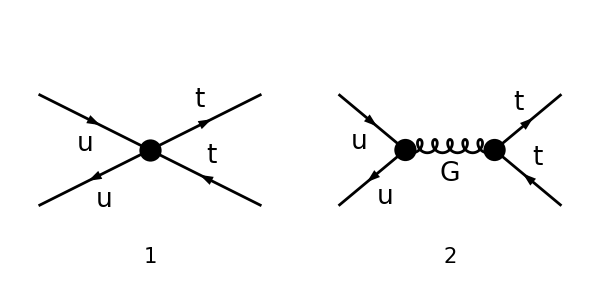

```mathematica
tops = CreateTopologies[0,2->2];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[2]}, GenericModel->"../Models/TopEFTonshell-FA/TopEFTonshell-FA_FC"];
Paint[allDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},List->False,DropSumOver->True,LorentzIndexNames-> {μ},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 2 Particles amplitudes

-ⅈ (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^Lor2.(φ(-p2,MT)) (g^Lor2μ/(p1+p2)^2+((1-ξ_(V(Gen5))) (p1+p2)^Lor2 (-p1-p2)^μ)/(((p1+p2)^2)^2)) T_Col2Col1^Glu5 T_Col3Col4^Glu5 GS^2+(ⅈ A0 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^Lor2.(γ·(p1+p2)).(γ̄)^6.(φ(-p2,MT)) (g^Lor2μ/(p1+p2)^2+((1-ξ_(V(Gen5))) (p1+p2)^Lor2 (-p1-p2)^μ)/(((p1+p2)^2)^2)) T_Col2Col1^Glu5 T_Col3Col4^Glu5 GS^2)/(2 √aS √π)+(ⅈ A0 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^Lor2.(γ·(p1+p2)).(γ̄)^7.(φ(-p2,MT)) (g^Lor2μ/(p1+p2)^2+((1-ξ_(V(Gen5))) (p1+p2)^Lor2 (-p1-p2)^μ)/(((p1+p2)^2)^2)) T_Col2Col1^Glu5 T_Col3Col4^Glu5 GS^2)/(2 √aS √π)-(ⅈ A0 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).(γ·(p1+p2)).γ^Lor2.(γ̄)^6.(φ(-p2,MT)) (g^Lor2μ/(p1+p2)^2+((1-ξ_(V(Gen5))) (p1+p2)^Lor2 (-p1-p2)^μ)/(((p1+p2)^2)^2)) T_Col2Col1^Glu5 T_Col3Col4^Glu5 GS^2)/(2 √aS √π)-(ⅈ A0 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).(γ·(p1+p2)).γ^Lor2.(γ̄)^7.(φ(-p2,MT)) (g^Lor2μ/(p1+p2)^2+((1-ξ_(V(Gen5))) (p1+p2)^Lor2 (-p1-p2)^μ)/(((p1+p2)^2)^2)) T_Col2Col1^Glu5 T_Col3Col4^Glu5 GS^2)/(2 √aS √π)+1/4 ⅈ B0 (φ(-k2)).γ^Ind96.(φ(k1)) (φ(p1,MT)).γ^Ind96.(γ̄)^6.(φ(-p2,MT)) (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4)

```mathematica
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

1/4 ⅈ (B0 (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4) (φ(-k2)).γ^Ind96.(φ(k1)) (φ(p1,MT)).γ^Ind96.(γ̄)^6.(φ(-p2,MT))-1/(√π √aS (p1+p2)^2)4 GS.GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 A0 MT (φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))-A0 ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))+√π √aS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT))))

```mathematica
FullSimplify[ampB-(ampB/.B0->0)]
```

1/4 ⅈ B0 (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4) (φ(-k2)).γ^Ind96.(φ(k1)) (φ(p1,MT)).γ^Ind96.(γ̄)^6.(φ(-p2,MT))

```mathematica
ampC=FCReplaceMomenta[ampB,{k->p1+p2}]
```

-(ⅈ GS T_Col2Col3^Glu1 (A0 (-γ^μ.(γ·p1+γ·p2).(γ̄)^6-γ^μ.(γ·p1+γ·p2).(γ̄)^7+(γ·p1+γ·p2).γ^μ.(γ̄)^6+(γ·p1+γ·p2).γ^μ.(γ̄)^7)+2 √π √aS γ^μ))/(2 √π √aS)

```mathematica
ampD = DiracSimplify[Expand[ExpandScalarProduct[ampC]]]
```

(ⅈ A0 GS T_Col2Col3^Glu1 γ^μ.(γ·p1).(γ̄)^6)/(2 √π √aS)+(ⅈ A0 GS T_Col2Col3^Glu1 γ^μ.(γ·p1).(γ̄)^7)/(2 √π √aS)-(ⅈ A0 GS T_Col2Col3^Glu1 (γ·p1).γ^μ.(γ̄)^6)/(2 √π √aS)-(ⅈ A0 GS T_Col2Col3^Glu1 (γ·p1).γ^μ.(γ̄)^7)/(2 √π √aS)+(ⅈ A0 GS T_Col2Col3^Glu1 γ^μ.(γ·p2).(γ̄)^6)/(2 √π √aS)+(ⅈ A0 GS T_Col2Col3^Glu1 γ^μ.(γ·p2).(γ̄)^7)/(2 √π √aS)-(ⅈ A0 GS T_Col2Col3^Glu1 (γ·p2).γ^μ.(γ̄)^6)/(2 √π √aS)-(ⅈ A0 GS T_Col2Col3^Glu1 (γ·p2).γ^μ.(γ̄)^7)/(2 √π √aS)-ⅈ GS γ^μ T_Col2Col3^Glu1

```mathematica
ampE = Expand[Collect[Simplify[( ampD)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},foo]]/.foo->FullSimplify
```

-ⅈ T_Col2Col3^Glu1 (A0 (-γ^μ.(γ·p1).(γ̄)^6-γ^μ.(γ·p1).(γ̄)^7+(γ·p1).γ^μ.(γ̄)^6+(γ·p1).γ^μ.(γ̄)^7-γ^μ.(γ·p2).(γ̄)^6-γ^μ.(γ·p2).(γ̄)^7+(γ·p2).γ^μ.(γ̄)^6+(γ·p2).γ^μ.(γ̄)^7)+GS γ^μ)

```mathematica
Expand[%]
```

ⅈ A0 T_Col2Col3^Glu1 γ^μ.(γ·p1).(γ̄)^6+ⅈ A0 T_Col2Col3^Glu1 γ^μ.(γ·p1).(γ̄)^7-ⅈ A0 T_Col2Col3^Glu1 (γ·p1).γ^μ.(γ̄)^6-ⅈ A0 T_Col2Col3^Glu1 (γ·p1).γ^μ.(γ̄)^7+ⅈ A0 T_Col2Col3^Glu1 γ^μ.(γ·p2).(γ̄)^6+ⅈ A0 T_Col2Col3^Glu1 γ^μ.(γ·p2).(γ̄)^7-ⅈ A0 T_Col2Col3^Glu1 (γ·p2).γ^μ.(γ̄)^6-ⅈ A0 T_Col2Col3^Glu1 (γ·p2).γ^μ.(γ̄)^7-ⅈ GS γ^μ T_Col2Col3^Glu1

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampF=Expand[Collect[ampE,{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[Momentum[p1,D],D],DiracGamma[Momentum[p2,D],D],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},foo]]/.foo->FullSimplify
```

-ⅈ T_Col2Col3^Glu1 (A0 (-γ^μ.(γ·p1).(γ̄)^6-γ^μ.(γ·p1).(γ̄)^7+(γ·p1).γ^μ.(γ̄)^6+(γ·p1).γ^μ.(γ̄)^7-γ^μ.(γ·p2).(γ̄)^6-γ^μ.(γ·p2).(γ̄)^7+(γ·p2).γ^μ.(γ̄)^6+(γ·p2).γ^μ.(γ̄)^7)+GS γ^μ)

```mathematica
ampG=ampF/.{C00eff->C00-2 MT^2(C1+C11+C12)-s/2 (C1+2 C12)}//Simplify
```

-ⅈ GS T_Col2Col3^Glu1 (γ^μ.(γ̄)^7+(2 π^2 C00 yDM^2+1) γ^μ.(γ̄)^6+π^2 yDM^2 p1^μ (2 (C1+C11+C12) (γ·p1).(γ̄)^6-(C1+2 C12) (γ·p1+γ·p2).(γ̄)^6)+π^2 yDM^2 p2^μ (2 (C1+C11+C12) (γ·p2).(γ̄)^6-(C1+2 C12) (γ·p1+γ·p2).(γ̄)^6))

```mathematica
Expand[Collect[DiracSimplify[Expand[ampG]],{C00,C11,C12,C1},foo]]/.foo->FullSimplify
```

-2 ⅈ π^2 C00 GS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1-ⅈ π^2 C1 GS yDM^2 (p1^μ-p2^μ) T_Col2Col3^Glu1 ((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6)-2 ⅈ π^2 C11 GS yDM^2 T_Col2Col3^Glu1 (p1^μ (γ·p1).(γ̄)^6+p2^μ (γ·p2).(γ̄)^6)+2 ⅈ π^2 C12 GS yDM^2 T_Col2Col3^Glu1 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6)-ⅈ GS (γ^μ.(γ̄)^6+γ^μ.(γ̄)^7) T_Col2Col3^Glu1

```mathematica
FullSimplify[%]
```

-ⅈ GS T_Col2Col3^Glu1 (γ^μ.(γ̄)^7+(2 π^2 C00 yDM^2+1) γ^μ.(γ̄)^6+π^2 yDM^2 ((γ·p2).(γ̄)^6 ((C1+2 C11) p2^μ-(C1+2 C12) p1^μ)+(γ·p1).(γ̄)^6 ((C1+2 C11) p1^μ-(C1+2 C12) p2^μ)))